```mathematica
functionsmat = {{a -b*x*(z^o/(k^o + z^o))},{c*(1-y)*(x^p/(l^p + x^p)) - d*y},{e*(1-z)*(y^q/(m^q+y^q)) - f*z}}//MatrixForm
```

(a-(b x z^o)/(k^o+z^o)
(c x^p (1-y))/(l^p+x^p)-d y
(e y^q (1-z))/(m^q+y^q)-f z)

```mathematica
MatrixForm[functionsmat]
```

(a-(b x z^o)/(k^o+z^o)
(c x^p (1-y))/(l^p+x^p)-d y
(e y^q (1-z))/(m^q+y^q)-f z)

```mathematica
variablesmat = {{x},{y},{z}}
```

{{x},{y},{z}}

```mathematica
JacobianMat = D[functionsmat, {Transpose[variablesmat]}]
```

{{{{-(b z^o)/(k^o+z^o),0,(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o)}}},{{{-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p),-d-(c x^p)/(l^p+x^p),0}}},{{{0,-(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q),-f-(e y^q)/(m^q+y^q)}}}}

```mathematica
JacobianMat//MatrixForm
```

((-(b z^o)/(k^o+z^o) | 0 | (b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o))
(-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p) | -d-(c x^p)/(l^p+x^p) | 0)
(0 | -(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q) | -f-(e y^q)/(m^q+y^q)))

```mathematica
Take[JacobianMat,{1}]
```

{{{{-(b z^o)/(k^o+z^o),0,(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o)}}}}

```mathematica
JacoMatFinal = {{{-(b z^o)/(k^o+z^o)},{0},{(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o)}},{{-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p)},{-d-(c x^p)/(l^p+x^p)},{0}},{{0},{-(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q)},{-f-(e y^q)/(m^q+y^q)}}}//MatrixForm
```

((-(b z^o)/(k^o+z^o)) | (0) | ((b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o))
(-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p)) | (-d-(c x^p)/(l^p+x^p)) | (0)
(0) | (-(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q)) | (-f-(e y^q)/(m^q+y^q)))

```mathematica
jmatrix = {-(b z^o)/(k^o+z^o),0,(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o),-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p),-d-(c x^p)/(l^p+x^p),0,0,-(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q),-f-(e y^q)/(m^q+y^q)}
```

{-(b z^o)/(k^o+z^o),0,(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o),-(c p x^(-1+2 p) (1-y))/((l^p+x^p)^2)+(c p x^(-1+p) (1-y))/(l^p+x^p),-d-(c x^p)/(l^p+x^p),0,0,-(e q y^(-1+2 q) (1-z))/((m^q+y^q)^2)+(e q y^(-1+q) (1-z))/(m^q+y^q),-f-(e y^q)/(m^q+y^q)}

```mathematica
Take[jmatrix, {1,3}]//MatrixForm
```

(-(b z^o)/(k^o+z^o)
0
(b o x z^(-1+2 o))/((k^o+z^o)^2)-(b o x z^(-1+o))/(k^o+z^o))

```mathematica
functionsmat2 = {{0.0125-6*x*(z^8/(0.2^8+z^8))},{1.5*(1-y)*(x^4/(0.3^4+x^4))-0.6*y},{1.5*(1-z)*(y^4/(0.3^4+y^4))-0.6*z}}
```

{{0.0125-(6 x z^8)/(2.56×10^-6+z^8)},{(1.5 x^4 (1-y))/(0.0081+x^4)-0.6 y},{(1.5 y^4 (1-z))/(0.0081+y^4)-0.6 z}}

```mathematica
variablesmatrix = Transpose[{{x},{y},{z}}]
```

{{x,y,z}}

```mathematica
jacobianmatrix2 = D[functionsmat2, {{x,y,z}}]//MatrixForm
```

```mathematica
({{({{-(6 z^8)/(2.56^-6+z^8)}, {0}, {(48 x z^15)/((2.56^-6+z^8)^2)-(48 x z^7)/(2.56^-6+z^8)}})}, {({{-(6. x^7 (1-y))/((0.0081+x^4)^2)+(6. x^3 (1-y))/(0.0081+x^4)}, {-0.6-(1.5 x^4)/(0.0081+x^4)}, {0}})}, {({{0}, {-(6. y^7 (1-z))/((0.0081+y^4)^2)+(6. y^3 (1-z))/(0.0081+y^4)}, {-0.6-(1.5 y^4)/(0.0081+y^4)}})}})
```

{{{-(6 z^8)/(0.00355271+z^8),0,((48 x z^15)/((0.00355271+z^8)^2)-(48 x z^7)/(0.00355271+z^8)) }},{{(-(6. x^7 (1-y))/((0.0081+x^4)^2)+(6. x^3 (1-y))/(0.0081+x^4)) ,(-0.6-(1.5 x^4)/(0.0081+x^4)) ,0}},{{0,(-(6. y^7 (1-z))/((0.0081+y^4)^2)+(6. y^3 (1-z))/(0.0081+y^4)) ,(-0.6-(1.5 y^4)/(0.0081+y^4)) }}}

```mathematica
jacobianmatrix3 = {{-0.0800756, 0, -0.844753},{2.08914, -0.702446, 0},{0, 1.82037, -0.679345}}
```

```mathematica
{{-0.0800756,0,-0.844753},{2.08914,-0.702446,0},{0,1.82037,-0.679345}}//MatrixForm
```

(-0.0800756 | 0 | -0.844753
2.08914 | -0.702446 | 0
0 | 1.82037 | -0.679345)

```mathematica
Eigenvalues[jacobianmatrix3]//MatrixForm
```

(-1.98842+0. ⅈ
0.263279+1.25122 ⅈ
0.263279-1.25122 ⅈ)

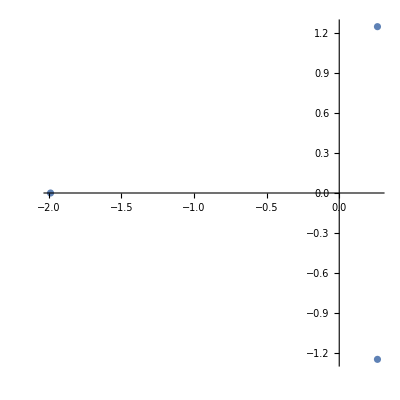

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{-1.988423884923382+0. ⅈ,0.26327864246169075+1.2512211474456418 ⅈ,0.26327864246169075-1.2512211474456418 ⅈ},AspectRatio->1]
```

```mathematica
({{({{-(6 z^8)/(2.56^-6+z^8)}, {0}, {(48 x z^15)/((2.56^-6+z^8)^2)-(48 x z^7)/(2.56^-6+z^8)}})}, {({{-(6. x^7 (1-y))/((0.0081+x^4)^2)+(6. x^3 (1-y))/(0.0081+x^4)}, {-0.6-(1.5 x^4)/(0.0081+x^4)}, {0}})}, {({{0}, {-(6. y^7 (1-z))/((0.0081+y^4)^2)+(6. y^3 (1-z))/(0.0081+y^4)}, {-0.6-(1.5 y^4)/(0.0081+y^4)}})}})//MatrixForm
```

((-(6 z^8)/(0.00355271+z^8)
0
(48 x z^15)/((0.00355271+z^8)^2)-(48 x z^7)/(0.00355271+z^8))
(-(6. x^7 (1-y))/((0.0081+x^4)^2)+(6. x^3 (1-y))/(0.0081+x^4)
-0.6-(1.5 x^4)/(0.0081+x^4)
0)
(0
-(6. y^7 (1-z))/((0.0081+y^4)^2)+(6. y^3 (1-z))/(0.0081+y^4)
-0.6-(1.5 y^4)/(0.0081+y^4)))

```mathematica
Transpose[%112,{1,2,3}]
```

{{{-(6 z^8)/(0.00355271+z^8),0,(48 x z^15)/((0.00355271+z^8)^2)-(48 x z^7)/(0.00355271+z^8)}},{{-(6. x^7 (1-y))/((0.0081+x^4)^2)+(6. x^3 (1-y))/(0.0081+x^4),-0.6-(1.5 x^4)/(0.0081+x^4),0}},{{0,-(6. y^7 (1-z))/((0.0081+y^4)^2)+(6. y^3 (1-z))/(0.0081+y^4),-0.6-(1.5 y^4)/(0.0081+y^4)}}}